13 Vectores
13.1 Operaciones con vectores

```mathematica
u={3,5,7}
v={2,-5,9}
```

{3,5,7}

{2,-5,9}

```mathematica
u+v
u-v
3u-5v
u*v
u^2
1/u
```

{5,0,16}

{1,10,-2}

{-1,40,-24}

{6,-25,63}

{9,25,49}

{1/3,1/5,1/7}

13.2 Dibujo de vectores

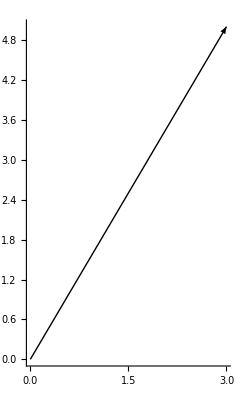

```mathematica
Graphics[Arrow[{{0,0},{3,5}}], Axes->True](* u=(3,5) *)
```

```mathematica
Graphics3D[Arrow[{{0,0,0},{2,3,1}}], Axes->True](* u=(2,3,1) *)
```

-Graphics3D-

13.3 Producto escalar y vectorial

```mathematica
u={2,3,2}
v={1,-2,1}
```

{2,3,2}

{1,-2,1}

Dados u y v, calcular u.v:

```mathematica
u.v
Dot[u,v]
```

-2

-2

Comprobar que el producto escalar de u consigo mismo es el cuadrado de la norma del vector:

```mathematica
u.u (* Producto escalar *)
Dot[u,u](* Producto escalar *)
Norm[u]^2 (* Norma de u *)
```

17

17

17

Calcular el ángulo que forman los vectores u y v entre sí:

```mathematica
VectorAngle[u,v]//N
```

1.77014

Calcula el producto vectorial o cruz de los vectores anteriores:

```mathematica
Cross[u,v]
Cross[u,u] (* Extra *)
Cross[v,v] (* Extra *)
```

{7,0,-7}

{0,0,0}

{0,0,0}

Comprueba que el producto cruz es ortogonal a cada u y v:

```mathematica
Cross[u,v].u
Cross[u,v].v
```

0

0

13.4 Proyección ortogonal

```mathematica
u
v
```

{2,3,2}

{1,-2,1}

Calcula la proyección p de u sobre v:

```mathematica
(u.v)/(v.v)v
p=Projection[u,v]
```

{-1/3,2/3,-1/3}

{-1/3,2/3,-1/3}

Comprobar que la proyección p y v son paralelas:

```mathematica
p/v (* Un vector es múltiplo del otro, son paralelos *)
```

{-1/3,-1/3,-1/3}

Comprueba que u-p es ortogonal a v:

```mathematica
(u-p).v
```

0

13.5 Ortogonalización de Gramm-Schmidt

```mathematica
u={2,4,5,7}
v={2,-5,8,9}
w={3,5,1,2}
```

{2,4,5,7}

{2,-5,8,9}

{3,5,1,2}

```mathematica
{a,b,c}=Orthogonalize[{u,v,w}]
```

{{√(2/47),2 √(2/47),5/(√94),7/(√94)},{7 √(2/412989),-409 √(2/412989),317/(√825978),79 √(3/275326)},{18433/(√356286489),-1234/(√356286489),-1262/(√356286489),-1220 √(3/118762163)}}

Comprobar el resultado:

```mathematica
a.b
a.c
b.c
```

0

0

0

```mathematica
Norm[a]
Norm[b]
Norm[c]
```

1

1

1

13.6 Comprobaciones con cálculo simbólico

```mathematica
u={u1,u2,u3}
v={v1,v2,v3}
```

{u1,u2,u3}

{v1,v2,v3}

El producto escalar es conmutativo:

```mathematica
u.v
v.u
u.v==v.u
```

u1 v1+u2 v2+u3 v3

u1 v1+u2 v2+u3 v3

True

u.u=u:

```mathematica
u.u
Norm[u]^2
u.u==Norm[u]^2
```

u1^2+u2^2+u3^2

Abs[u1]^2+Abs[u2]^2+Abs[u3]^2

u1^2+u2^2+u3^2==Abs[u1]^2+Abs[u2]^2+Abs[u3]^2

El producto cruz es anticonmutativo:

```mathematica
Cross[u,v]
Cross[v,u]
Cross[u,v]==-Cross[v,u]
```

{-u3 v2+u2 v3,u3 v1-u1 v3,-u2 v1+u1 v2}

{u3 v2-u2 v3,-u3 v1+u1 v3,u2 v1-u1 v2}

True

El producto cruz es ortogonal a los vectores u y v:

```mathematica
Cross[u,v].u//Simplify
Cross[u,v].v//Simplify
-Cross[u,v].u//Simplify
-Cross[u,v].u//Simplify
```

0

0

0

«1 more identical outputs»

13.7 Generación de sucesiones aritméticas
Crear un vector con números del 1 al 9:

```mathematica
Range[1,9]
```

{1,2,3,4,5,6,7,8,9}

Crear un vector con números del 5 al 13:

```mathematica
Range[5,13]
```

{5,6,7,8,9,10,11,12,13}

Crear un vector con números del 5 al 6 con incrementos de 0.1:

```mathematica
Range[5,6,0.1]
```

{5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.}

Crear un vector con el cubo de los primeros siete números:

```mathematica
Table[n^3,{n,1,7}]
```

{1,8,27,64,125,216,343}

13.8 Indexación de vectores

```mathematica
v={4,0,8,5,4,6,7,1}
```

{4,0,8,5,4,6,7,1}

Mostrar la tercera componente y la segunda empezando por el final:

```mathematica
v[[3]]
v[[-2]]
```

8

7

Cambiar el valor de la segunda componente por 90:

```mathematica
v[[2]]=90
v
```

90

{4,90,8,5,4,6,7,1}

Extraer partes del vector

```mathematica
v[[2;;5]]
Part[v,3]
Part[v,2;;6]
```

{90,8,5,4}

8

{90,8,5,4,6}